# Converting Yasasya’s Files

There are two matrix files from in this directory that are not in a particularly portable form.  I should really convert them to the portable “mtx” form we looked at. Instead I am just going to read work out how to read them into Mathematica: I want to understand what they look like.

## Matrix 1

Matrix1.txt

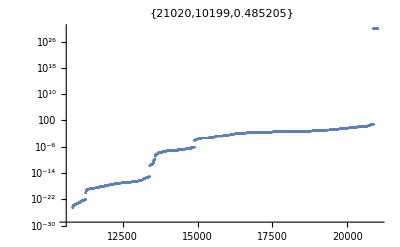

SparseArray[<10199>, {410, 410}]

SparseArray[<10199>, {410, 410}]

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\5631\\SampleMatrices"];
fStream=OpenRead["Matrix1.txt"];
(* Skip the Header *)
Skip[fStream,"String",2]
(* Read Dimensions and count *)
{n,m,nz}=Read[fStream,{Number,Number,Number}];
(* Tidy up the end iof the line *)
Skip[fStream,"String"];
(* read the data *)
Y1 = Partition[ReadList[fStream,Number],3]/.{i_,j_,z_}:>{i+1,j+1}->z;
Close[fStream]
(* Purge the Zeros *)
Y1F=Select[Y1, Abs[#⟦2⟧]>0 &];
(* inspect nonzero entries and count non-zeros *)
{nnz1,nnzF}=Map[Length,{Y1,Y1F}];
ListLogPlot[Sort[Abs[Y1⟦All,2⟧]],PlotRange->All,
PlotLabel->{nnz1,nnzF, N[nnzF/nnz1]}]
(* Build Sparse Matrices *)
Y1=SparseArray[Y1,{n,m}]
Y1F=SparseArray[Y1F,{n,m}]
(* Dump output as mtx *)
Export["Y1.mtx",Y1];
Export["Y1F.mtx",Y1F];
```

I just learned that Mathematica automatically prunes the “stored” zeros.  Not sure how I feel about that! Here is the spectrum.

```mathematica
SymTest=Norm[Y1-Transpose[Y1],"Frobenius"];
λs=Select[Eigenvalues[Normal[Y1]],Norm[#]<10^29&];
Norm[Im[λs]]
TabView[{
"Y1"->MatrixPlot[Y1,PlotLabel->{SymTest,SymTest/Norm[Y1,"Frobenius"]},PlotLegends->Automatic],
"Y1-Y1ᵀ"->MatrixPlot[Y1-Transpose[Y1],PlotLabel->{SymTest,SymTest/Norm[Y1,"Frobenius"]},PlotLegends->Automatic],
"λs"->ListPlot[Sort[λs]],
"|λs|"->ListLogPlot[Sort[Abs[λs]]],
"|λs|_(3 : 60)"->ListLogPlot[Sort[Abs[λs]]⟦3;;60⟧],
"|λs|_(61 : end)"->ListLogPlot[Sort[Abs[λs]]⟦61;;-1⟧]
}]
```

0

123456